## Nonlinear Differential Equations

In this notebook, we solve nonlinear differential equations, looking at the time dependence, phase space plots, Poincare sections, and the power spectrum.

The notebook starts with the Duffing equation.  Your job is to modify it to the damped, driven pendulum, then to reproduce and extend the results from session 8 (which used diffeq_pendulum.cpp).

## Define the Differential Equation

Name the equation "diffeq".  Note the "==" in defining the equation.

```mathematica
diffeq := x''[t]+2 γ x'[t]+α  x[t]+β x[t]^3==fext Cos[ωext t]
```

Choose among the parameters:

```mathematica
p1 := {α =-1,β=1,ωext=1, γ=0.25,fext=0.34875};
```

```mathematica
p1
```

{-1,1,1,0.25,0.34875}

Choose among the initial conditions:

```mathematica
ic1 := {x0=1,v0=0.};
```

```mathematica
ic1
```

{1,0.}

## Solve the Differential Equation

Specify the range in time over which we will solve the differential equation.  We won't be able to use the solution outside of this range. (I.e., we'll have to extend this range if we get an "outside of range" error later.)

```mathematica
tmin=0; tmax=1000;
```

Numerically solve the differential equaiton using NDSolve, specifying the initial conditions.  Setting MaxSteps to a large number is needed if tmax is large.

```mathematica
solution = NDSolve[{diffeq,x[0]==x0, x'[0]==v0},x,{t,tmin,tmax},MaxSteps->20000];
```

NDSolve returns an "interpolating function", which can be evaluated later at any time t in tmin < t < tmax.

## Plot the Time Dependence and Phase Space

We can just use "Plot" with Evaluate and the "interpolating function" defined by "solution".

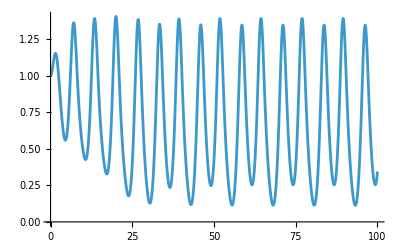

```mathematica
Plot[Evaluate[x[t]/.solution],{t,0,100}]
```

Or we can do a parametric plot ("ParametricPlot") with the same solution.  We've added various options here to (try to) make a nicer plot.

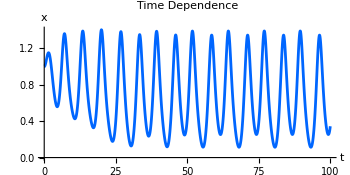

```mathematica
ParametricPlot[Evaluate[{t,x[t]}/.solution],{t,0,100},PlotStyle->Hue[0.6],BaseStyle->{FontFamily->"Times",FontSize->14},ImageSize->{350,200},PlotLabel->Style["Time Dependence"],AxesLabel->{"t","x"},AspectRatio->1/2]
```

Now do the phase space plot.  You may need to change AxesOrigin to get the axes in a reasonable place.

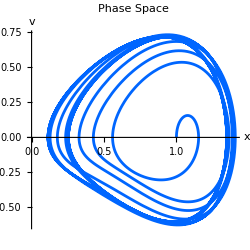

```mathematica
ParametricPlot[Evaluate[{x[t],x'[t]}/.solution],{t,tmin,100},PlotStyle->Hue[0.6],AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14},ImageSize->{250,200},PlotLabel->Style["Phase Space"],AxesOrigin->{Automatic,Automatic},AxesLabel->{"x","v"}]
```

Here is the same plot, with the starting time t set to skip the transient region.

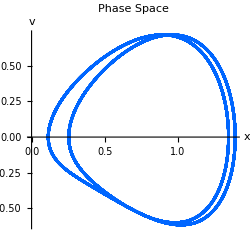

```mathematica
ParametricPlot[Evaluate[{x[t],x'[t]}/.solution],{t,100,300},PlotStyle->Hue[0.6],AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14},ImageSize->{250,200},PlotLabel->Style["Phase Space"],AxesOrigin->{Automatic,Automatic},AxesLabel->{"x","v"}]
```

## Poincare Sections

The idea of a Poincare section is to plot a point in phase space once every period of the external force, 2π/(external frequency).  The resulting pattern gives information about the periodicity of the signal (or indicates chaos).  Start the plot at a large enough time t ("tstart") so that the transients have died out.

Set the external period and how many periods we'll consider.  Define a function timeperiod[i] giving the corresponding time as a function of the period number.

```mathematica
Texternal := 2 Pi/ωext;
```

```mathematica
tstart = 40Texternal;
```

```mathematica
numperiods = 20;
```

```mathematica
timeperiod[i_] := tstart + i*Texternal
```

Just evaluate at the relevant points.  Flatten[expr,1] strips off a layer of {}'s.

```mathematica
PoincarePts = Flatten[Table[Evaluate[{x[timeperiod[i]],x'[timeperiod[i]]}/.solution],{i,0,numperiods}],1];
```

ListPlot plots pairs of numbers in the PlotRange.

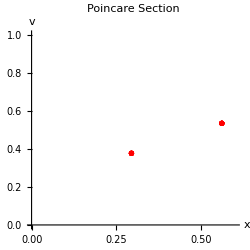

```mathematica
ListPlot[PoincarePts,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14},ImageSize->{250,200},PlotRange->{{0,0.6},{0,1}},PlotLabel->Style["Poincare Section"],AxesOrigin->Automatic,AxesLabel->{"x","v"},PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}]
```

## Power Spectrum

The power spectrum is found by taking a Fourier transform (FFT) of the signal.  We generate points at the same time intervals as in diffeq_pendulum.cpp.

```mathematica
Tskip = 100;
```

```mathematica
time[i_]:=tstart+i*Texternal/Tskip
```

```mathematica
numpoints = 5000;
```

```mathematica
SampleTime := numpoints * Texternal/Tskip
```

```mathematica
SamplePts=Flatten[Table[Evaluate[x[time[i]]/.solution],{i,0,numpoints}],1];
```

Check first that the plot still looks ok.

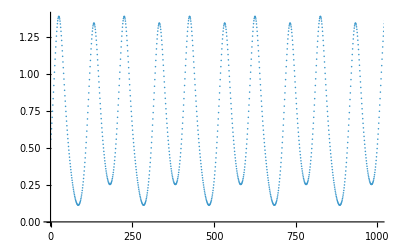

```mathematica
ListPlot[SamplePts,PlotRange->{{0,1000},Automatic}]
```

The basic command is Fourier.  FourierParameters chooses a particular convention for defining the transform.  Abs takes the magnitude of the resulting complex number (which we then square).

```mathematica
CenteredPts=SamplePts-Mean[SamplePts];
transform=Abs[Fourier[CenteredPts,FourierParameters->{-1,1}]]^2;
```

```mathematica
frequencies=Table[(2Pi/SampleTime)*i,{i,0,numpoints}];
```

Transpose to make pairs of points from two separate lists of points.

```mathematica
PlotPts = Transpose[{frequencies,transform}];
```

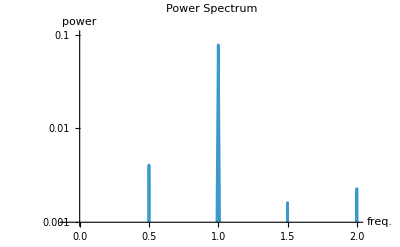

```mathematica
ListLogPlot[PlotPts,Joined->True,PlotRange->{{-0.1,2},{0.001,0.1}},BaseStyle->{FontFamily->"Times",FontSize->14},ImageSize->{400,300},PlotLabel->Style["Power Spectrum"],AxesOrigin->Automatic,AxesLabel->{"freq.","power"}]
```